### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
𝒞[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2,M1->M3,M3->M1,M2->M4,M4->M2}]
𝒫[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2,ϕ1->ϕ2,ϕ2->ϕ1,ϕ3->ϕ4,ϕ4->ϕ3,M1->M2,M2->M1,M3->M4,M4->M3}]
ℛ[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->ω1/ω2,ω2->1/ω2,ϕ3->ϕ4,ϕ4->ϕ3,M3->M4,M4->M3}]
𝒮[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1,ϕ1->ϕ4,ϕ4->ϕ1,ϕ2->ϕ3,ϕ3->ϕ2,M1->M4,M4->M1,M2->M3,M3->M2}]
```

```mathematica
EXPR[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]=Simplify[(#+𝒫@#+𝒞@#+ℛ@#+𝒫@𝒞@#+ℛ@𝒞@#+ℛ@𝒫@#+ℛ@𝒫@𝒞@#)&@ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]+(#+ℛ@#)&@ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]];
```

```mathematica
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]
```

ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]+ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][M3,M4,M2,M1]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]+ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]+ℳ0[1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][M4,M3,M1,M2]+ℳ0[((1-ω1+ω2) (1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2)))/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]+ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]:=If[ω2≥ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],0]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]);
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]:=If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0];
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]:=If[ω2>ω1,-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]),0];
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]:=If[(ω2>ω1)&&(ω1>1),-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}],0];
```

```mathematica
EXPR1[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md];
```

```mathematica
ℳone[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR1[ω1,ω2][Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine,Mseq},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"Yes"->True,"No"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Mseq=Sequence[M1,M2,M3,M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
{Ssqur,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]},{Ssqur,M1+M2,M1+M2+5,0.05}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

Function structure is Msum[<one flavour quark mass>][(excited state)<1>,<2>,<3>,<4>]

```mathematica
EXPR[ω1,ω2][M1,M2,M3,M4][ϕ1,ϕ2,ϕ3,ϕ4]
```

If[1/ω2>ω1/ω2&&ω1/ω2>1,-((4 π) NIntegrate[(M3^2+M4^2/(1/ω2)+M1^2/(x-ω1/ω2)+M1^2/(x-1)-M1^2/(x-ω1/ω2+1/ω2)-M1^2/x) ϕ1[(x-ω1/ω2+1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[x/(ω1/ω2)] ϕ3[x] ϕ4[(x-ω1/ω2+1/ω2)/(1/ω2)],{x,0,1}])/Nc,0]+If[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1,-1/Nc(4 π) NIntegrate[(M3^2+M4^2/(1/ω2)+M1^2/(x-(1-ω1+ω2)/ω2)+M1^2/(x-1)-M1^2/(x-(1-ω1+ω2)/ω2+1/ω2)-M1^2/x) ϕ1[(x-(1-ω1+ω2)/ω2+1/ω2)/(1+1/ω2-(1-ω1+ω2)/ω2)] ϕ2[x/((1-ω1+ω2)/ω2)] ϕ3[x] ϕ4[(x-(1-ω1+ω2)/ω2+1/ω2)/(1/ω2)],{x,0,1}],0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2)&&1/((1+1/ω2-ω1/ω2) ω2)>1,-1/Nc(4 π) NIntegrate[(M3^2+M4^2/(ω1/((1+1/ω2-ω1/ω2) ω2))+M1^2/(x-1/((1+1/ω2-ω1/ω2) ω2))+M1^2/(x-1)-M1^2/(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))-M1^2/x) ϕ1[(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[x/(1/((1+1/ω2-ω1/ω2) ω2))] ϕ3[x] ϕ4[(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))],{x,0,1}],0]+If[ω2>ω1&&ω1>1,-((4 π) NIntegrate[(M3^2+M4^2/ω2+M1^2/(x-ω1)+M1^2/(x-1)-M1^2/(x-ω1+ω2)-M1^2/x) ϕ1[(x-ω1+ω2)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[(x-ω1+ω2)/ω2],{x,0,1}])/Nc,0]+If[ω2>(1+1/ω2-ω1/ω2) ω2&&(1+1/ω2-ω1/ω2) ω2>1,-1/Nc(4 π) NIntegrate[(M3^2+M4^2/ω2+M1^2/(x-(1+1/ω2-ω1/ω2) ω2)+M1^2/(x-1)-M1^2/(x-(1+1/ω2-ω1/ω2) ω2+ω2)-M1^2/x) ϕ1[(x-(1+1/ω2-ω1/ω2) ω2+ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)] ϕ2[x/((1+1/ω2-ω1/ω2) ω2)] ϕ3[x] ϕ4[(x-(1+1/ω2-ω1/ω2) ω2+ω2)/ω2],{x,0,1}],0]+If[((1+1/ω2-ω1/ω2) ω2)/ω1>ω2/ω1&&ω2/ω1>1,-1/Nc(4 π) NIntegrate[(M3^2+M4^2/(((1+1/ω2-ω1/ω2) ω2)/ω1)+M1^2/(x-ω2/ω1)+M1^2/(x-1)-M1^2/(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)-M1^2/x) ϕ1[(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)/(1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1)] ϕ2[x/(ω2/ω1)] ϕ3[x] ϕ4[(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)/(((1+1/ω2-ω1/ω2) ω2)/ω1)],{x,0,1}],0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2)&&ω2/(1-ω1+ω2)>1,-1/Nc(4 π) NIntegrate[(M3^2+M4^2/(ω1/(1-ω1+ω2))+M1^2/(x-ω2/(1-ω1+ω2))+M1^2/(x-1)-M1^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-M1^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}],0]+If[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1,-1/Nc(4 π) NIntegrate[(M3^2+M4^2/((1-ω1+ω2)/ω1)+M1^2/(x-1/ω1)+M1^2/(x-1)-M1^2/(x-1/ω1+(1-ω1+ω2)/ω1)-M1^2/x) ϕ1[(x-1/ω1+(1-ω1+ω2)/ω1)/(1+(1-ω1+ω2)/ω1-1/ω1)] ϕ2[x/(1/ω1)] ϕ3[x] ϕ4[(x-1/ω1+(1-ω1+ω2)/ω1)/((1-ω1+ω2)/ω1)],{x,0,1}],0]+If[1>1/ω1,-4 g^2 (NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[y] ϕ3[y/ω1] ϕ4[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,0,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)-λ}]+NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[y] ϕ3[y/ω1] ϕ4[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)+λ,1}]-(2 NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)] ϕ3[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(ω1/ω1)] ϕ4[x])/(ω1/ω1),{x,0,1}])/λ),0]+If[1>ω1,-4 g^2 (NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-(2 NIntegrate[(ω2 ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[(ω1-ω2+x ω2)/ω1] ϕ3[((ω1-ω2+x ω2) ω1)/ω1] ϕ4[x])/ω1,{x,0,1}])/λ),0]+If[1>ω1/ω2,-4 g^2 (NIntegrate[(ω1 ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[y] ϕ3[(y ω1)/ω2] ϕ4[x])/(ω2 ω2 (((y-1) ω1)/ω2+(1-x)/ω2)^2),{x,0,1},{y,0,(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)-λ}]+NIntegrate[(ω1 ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[y] ϕ3[(y ω1)/ω2] ϕ4[x])/(ω2 ω2 (((y-1) ω1)/ω2+(1-x)/ω2)^2),{x,0,1},{y,(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)+λ,1}]-(2 NIntegrate[(ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)] ϕ3[((ω1/ω2-1/ω2+x/ω2) ω1)/((ω1 ω2)/ω2)] ϕ4[x])/((ω2 ω1)/ω2),{x,0,1}])/λ),0]+If[1>ω2/ω1,-4 g^2 (NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[y] ϕ3[(y ω2)/ω1] ϕ4[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,0,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)-λ}]+NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[y] ϕ3[(y ω2)/ω1] ϕ4[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)+λ,1}]-1/λ 2 NIntegrate[1/((ω1 ω2)/ω1)((1+1/ω2-ω1/ω2) ω2) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)] ϕ3[((ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1) ω2)/((ω2 ω1)/ω1)] ϕ4[x],{x,0,1}]),0]+If[1/ω2>ω1/ω2,-4 g^2 (NIntegrate[(ω1 ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω2 ((y ω1)/ω2-x)^2),{x,0,1},{y,0,x/(ω1/ω2)-λ}]+NIntegrate[(ω1 ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω2 ((y ω1)/ω2-x)^2),{x,0,1},{y,x/(ω1/ω2)+λ,1}]-(2 NIntegrate[(ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[x/(ω1/ω2)] ϕ3[x] ϕ4[(((x/(ω1/ω2)-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω1/ω2),{x,0,1}])/λ),0]+If[1/ω2>ω1/ω2,(4 g^2 ω1 NIntegrate[(ϕ1[(1/ω2-ω1/ω2+x)/(1/ω2-ω1/ω2+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω1)/(ω2/ω2)])/((y ω1)/ω2-1/ω2-x)^2,{x,0,1},{y,0,1}])/ω2,0]+If[1/ω2>(1-ω1+ω2)/ω2,(4 g^2 (1-ω1+ω2) NIntegrate[(ϕ1[(1/ω2-(1-ω1+ω2)/ω2+x)/(1/ω2-(1-ω1+ω2)/ω2+1)] ϕ2[y] ϕ3[x] ϕ4[(y (1-ω1+ω2))/(ω2/ω2)])/((y (1-ω1+ω2))/ω2-1/ω2-x)^2,{x,0,1},{y,0,1}])/ω2,0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2),-4 g^2 (NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[y] ϕ3[x] ϕ4[((y-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(((1+1/ω2-ω1/ω2) ω2) (y/((1+1/ω2-ω1/ω2) ω2)-x)^2),{x,0,1},{y,0,x/(1/((1+1/ω2-ω1/ω2) ω2))-λ}]+NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[y] ϕ3[x] ϕ4[((y-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(((1+1/ω2-ω1/ω2) ω2) (y/((1+1/ω2-ω1/ω2) ω2)-x)^2),{x,0,1},{y,x/(1/((1+1/ω2-ω1/ω2) ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[x/(1/((1+1/ω2-ω1/ω2) ω2))] ϕ3[x] ϕ4[((x/(1/((1+1/ω2-ω1/ω2) ω2))-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(1/((1+1/ω2-ω1/ω2) ω2)),{x,0,1}])/λ),0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2),(4 g^2 NIntegrate[(ϕ1[(ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2)+x)/(ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2)+1)] ϕ2[y] ϕ3[x] ϕ4[y/((((1+1/ω2-ω1/ω2) ω2) ω1)/((1+1/ω2-ω1/ω2) ω2))])/(y/((1+1/ω2-ω1/ω2) ω2)-ω1/((1+1/ω2-ω1/ω2) ω2)-x)^2,{x,0,1},{y,0,1}])/((1+1/ω2-ω1/ω2) ω2),0]+If[ω2>ω1,-4 g^2 (NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,x/ω1+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,0,1}])/λ),0]+If[ω2>ω1,4 g^2 ω1 NIntegrate[(ϕ1[(ω2-ω1+x)/(ω2-ω1+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω1)/ω2])/(y ω1-ω2-x)^2,{x,0,1},{y,0,1}],0]+If[ω2>(1+1/ω2-ω1/ω2) ω2,4 g^2 ((1+1/ω2-ω1/ω2) ω2) NIntegrate[(ϕ1[(ω2-(1+1/ω2-ω1/ω2) ω2+x)/(ω2-(1+1/ω2-ω1/ω2) ω2+1)] ϕ2[y] ϕ3[x] ϕ4[(y ((1+1/ω2-ω1/ω2) ω2))/ω2])/(y ((1+1/ω2-ω1/ω2) ω2)-ω2-x)^2,{x,0,1},{y,0,1}],0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2),-4 g^2 (NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2),(4 g^2 ω2 NIntegrate[(ϕ1[(ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2)+x)/(ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2)+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω2)/(((1-ω1+ω2) ω1)/(1-ω1+ω2))])/((y ω2)/(1-ω1+ω2)-ω1/(1-ω1+ω2)-x)^2,{x,0,1},{y,0,1}])/(1-ω1+ω2),0]+If[((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)>ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2),1/(1+ω2-(1+1/ω2-ω1/ω2) ω2)4 g^2 ω2 NIntegrate[(ϕ1[(((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2)+x)/(((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2)+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω2)/(((1+ω2-(1+1/ω2-ω1/ω2) ω2) ((1+1/ω2-ω1/ω2) ω2))/(1+ω2-(1+1/ω2-ω1/ω2) ω2))])/((y ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-x)^2,{x,0,1},{y,0,1}],0]+If[(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))>1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))4 g^2 NIntegrate[(ϕ1[((1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))+x)/((1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))+1)] ϕ2[y] ϕ3[x] ϕ4[y/(((ω2 (1+1/ω2-(1-ω1+ω2)/ω2)) (1-ω1+ω2))/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)))])/(y/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-x)^2,{x,0,1},{y,0,1}],0]

```mathematica
Msumdat=Msum[60][2,2,0,0]
```

```mathematica
?EXPR1
```

Global`EXPR1

EXPR1[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=If[1/ω2>ω1/ω2&&ω1/ω2>1,-((4 π) NIntegrate[(Mc^2+Md^2/(1/ω2)+Ma^2/(x-ω1/ω2)+Ma^2/(x-1)-Ma^2/(x-ω1/ω2+1/ω2)-Ma^2/x) ϕ1[(x-ω1/ω2+1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[x/(ω1/ω2)] ϕ3[x] ϕ4[(x-ω1/ω2+1/ω2)/(1/ω2)],{x,0,1}])/Nc,0]+If[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1,-((4 π) NIntegrate[(Mc^2+Md^2/(1/ω2)+Ma^2/(x-(1-ω1+ω2)/ω2)+Ma^2/(x-1)-Ma^2/(x-(1-ω1+ω2)/ω2+1/ω2)-Ma^2/x) ϕ1[(x-(1-ω1+ω2)/ω2+1/ω2)/(1+1/ω2-(1-ω1+ω2)/ω2)] ϕ2[x/((1-ω1+ω2)/ω2)] ϕ3[x] ϕ4[(x-(1-ω1+ω2)/ω2+1/ω2)/(1/ω2)],{x,0,1}])/Nc,0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2)&&1/((1+1/ω2-ω1/ω2) ω2)>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(ω1/((1+1/ω2-ω1/ω2) ω2))+Ma^2/(x-1/((1+1/ω2-ω1/ω2) ω2))+Ma^2/(x-1)-Ma^2/(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))-Ma^2/x) ϕ1[(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[x/(1/((1+1/ω2-ω1/ω2) ω2))] ϕ3[x] ϕ4[(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))],{x,0,1}],0]+If[ω2>ω1&&ω1>1,-((4 π) NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x) ϕ1[(x-ω1+ω2)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[(x-ω1+ω2)/ω2],{x,0,1}])/Nc,0]+If[ω2>(1+1/ω2-ω1/ω2) ω2&&(1+1/ω2-ω1/ω2) ω2>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-(1+1/ω2-ω1/ω2) ω2)+Ma^2/(x-1)-Ma^2/(x-(1+1/ω2-ω1/ω2) ω2+ω2)-Ma^2/x) ϕ1[(x-(1+1/ω2-ω1/ω2) ω2+ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)] ϕ2[x/((1+1/ω2-ω1/ω2) ω2)] ϕ3[x] ϕ4[(x-(1+1/ω2-ω1/ω2) ω2+ω2)/ω2],{x,0,1}],0]+If[((1+1/ω2-ω1/ω2) ω2)/ω1>ω2/ω1&&ω2/ω1>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(((1+1/ω2-ω1/ω2) ω2)/ω1)+Ma^2/(x-ω2/ω1)+Ma^2/(x-1)-Ma^2/(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)-Ma^2/x) ϕ1[(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)/(1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1)] ϕ2[x/(ω2/ω1)] ϕ3[x] ϕ4[(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)/(((1+1/ω2-ω1/ω2) ω2)/ω1)],{x,0,1}],0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2)&&ω2/(1-ω1+ω2)>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(ω1/(1-ω1+ω2))+Ma^2/(x-ω2/(1-ω1+ω2))+Ma^2/(x-1)-Ma^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-Ma^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}],0]+If[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1,-((4 π) NIntegrate[(Mc^2+Md^2/((1-ω1+ω2)/ω1)+Ma^2/(x-1/ω1)+Ma^2/(x-1)-Ma^2/(x-1/ω1+(1-ω1+ω2)/ω1)-Ma^2/x) ϕ1[(x-1/ω1+(1-ω1+ω2)/ω1)/(1+(1-ω1+ω2)/ω1-1/ω1)] ϕ2[x/(1/ω1)] ϕ3[x] ϕ4[(x-1/ω1+(1-ω1+ω2)/ω1)/((1-ω1+ω2)/ω1)],{x,0,1}])/Nc,0]+If[1>1/ω1,-4 g^2 (NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[y] ϕ3[y/ω1] ϕ4[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,0,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)-λ}]+NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[y] ϕ3[y/ω1] ϕ4[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)+λ,1}]-(2 NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)] ϕ3[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(ω1/ω1)] ϕ4[x])/(ω1/ω1),{x,0,1}])/λ),0]+If[1>ω1,-4 g^2 (NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-(2 NIntegrate[(ω2 ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[(ω1-ω2+x ω2)/ω1] ϕ3[((ω1-ω2+x ω2) ω1)/ω1] ϕ4[x])/ω1,{x,0,1}])/λ),0]+If[1>ω1/ω2,-4 g^2 (NIntegrate[(ω1 ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[y] ϕ3[(y ω1)/ω2] ϕ4[x])/(ω2 ω2 (((y-1) ω1)/ω2+(1-x)/ω2)^2),{x,0,1},{y,0,(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)-λ}]+NIntegrate[(ω1 ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[y] ϕ3[(y ω1)/ω2] ϕ4[x])/(ω2 ω2 (((y-1) ω1)/ω2+(1-x)/ω2)^2),{x,0,1},{y,(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)+λ,1}]-(2 NIntegrate[(ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)] ϕ3[((ω1/ω2-1/ω2+x/ω2) ω1)/((ω1 ω2)/ω2)] ϕ4[x])/((ω2 ω1)/ω2),{x,0,1}])/λ),0]+If[1>ω2/ω1,-4 g^2 (NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[y] ϕ3[(y ω2)/ω1] ϕ4[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,0,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)-λ}]+NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[y] ϕ3[(y ω2)/ω1] ϕ4[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)+λ,1}]-1/λ 2 NIntegrate[1/((ω1 ω2)/ω1)((1+1/ω2-ω1/ω2) ω2) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)] ϕ3[((ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1) ω2)/((ω2 ω1)/ω1)] ϕ4[x],{x,0,1}]),0]+If[1/ω2>ω1/ω2,-4 g^2 (NIntegrate[(ω1 ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω2 ((y ω1)/ω2-x)^2),{x,0,1},{y,0,x/(ω1/ω2)-λ}]+NIntegrate[(ω1 ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω2 ((y ω1)/ω2-x)^2),{x,0,1},{y,x/(ω1/ω2)+λ,1}]-(2 NIntegrate[(ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[x/(ω1/ω2)] ϕ3[x] ϕ4[(((x/(ω1/ω2)-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω1/ω2),{x,0,1}])/λ),0]+If[1/ω2>ω1/ω2,(4 g^2 ω1 NIntegrate[(ϕ1[(1/ω2-ω1/ω2+x)/(1/ω2-ω1/ω2+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω1)/(ω2/ω2)])/((y ω1)/ω2-1/ω2-x)^2,{x,0,1},{y,0,1}])/ω2,0]+If[1/ω2>(1-ω1+ω2)/ω2,(4 g^2 (1-ω1+ω2) NIntegrate[(ϕ1[(1/ω2-(1-ω1+ω2)/ω2+x)/(1/ω2-(1-ω1+ω2)/ω2+1)] ϕ2[y] ϕ3[x] ϕ4[(y (1-ω1+ω2))/(ω2/ω2)])/((y (1-ω1+ω2))/ω2-1/ω2-x)^2,{x,0,1},{y,0,1}])/ω2,0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2),-4 g^2 (NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[y] ϕ3[x] ϕ4[((y-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(((1+1/ω2-ω1/ω2) ω2) (y/((1+1/ω2-ω1/ω2) ω2)-x)^2),{x,0,1},{y,0,x/(1/((1+1/ω2-ω1/ω2) ω2))-λ}]+NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[y] ϕ3[x] ϕ4[((y-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(((1+1/ω2-ω1/ω2) ω2) (y/((1+1/ω2-ω1/ω2) ω2)-x)^2),{x,0,1},{y,x/(1/((1+1/ω2-ω1/ω2) ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[x/(1/((1+1/ω2-ω1/ω2) ω2))] ϕ3[x] ϕ4[((x/(1/((1+1/ω2-ω1/ω2) ω2))-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(1/((1+1/ω2-ω1/ω2) ω2)),{x,0,1}])/λ),0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2),(4 g^2 NIntegrate[(ϕ1[(ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2)+x)/(ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2)+1)] ϕ2[y] ϕ3[x] ϕ4[y/((((1+1/ω2-ω1/ω2) ω2) ω1)/((1+1/ω2-ω1/ω2) ω2))])/(y/((1+1/ω2-ω1/ω2) ω2)-ω1/((1+1/ω2-ω1/ω2) ω2)-x)^2,{x,0,1},{y,0,1}])/((1+1/ω2-ω1/ω2) ω2),0]+If[ω2>ω1,-4 g^2 (NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,x/ω1+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,0,1}])/λ),0]+If[ω2>ω1,4 g^2 ω1 NIntegrate[(ϕ1[(ω2-ω1+x)/(ω2-ω1+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω1)/ω2])/(y ω1-ω2-x)^2,{x,0,1},{y,0,1}],0]+If[ω2>(1+1/ω2-ω1/ω2) ω2,4 g^2 ((1+1/ω2-ω1/ω2) ω2) NIntegrate[(ϕ1[(ω2-(1+1/ω2-ω1/ω2) ω2+x)/(ω2-(1+1/ω2-ω1/ω2) ω2+1)] ϕ2[y] ϕ3[x] ϕ4[(y ((1+1/ω2-ω1/ω2) ω2))/ω2])/(y ((1+1/ω2-ω1/ω2) ω2)-ω2-x)^2,{x,0,1},{y,0,1}],0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2),-4 g^2 (NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2),(4 g^2 ω2 NIntegrate[(ϕ1[(ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2)+x)/(ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2)+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω2)/(((1-ω1+ω2) ω1)/(1-ω1+ω2))])/((y ω2)/(1-ω1+ω2)-ω1/(1-ω1+ω2)-x)^2,{x,0,1},{y,0,1}])/(1-ω1+ω2),0]+If[((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)>ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2),(4 g^2 ω2 NIntegrate[(ϕ1[(((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2)+x)/(((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2)+1)] ϕ2[y] ϕ3[x] ϕ4[(y ω2)/(((1+ω2-(1+1/ω2-ω1/ω2) ω2) ((1+1/ω2-ω1/ω2) ω2))/(1+ω2-(1+1/ω2-ω1/ω2) ω2))])/((y ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)-x)^2,{x,0,1},{y,0,1}])/(1+ω2-(1+1/ω2-ω1/ω2) ω2),0]+If[(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))>1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),(4 g^2 NIntegrate[(ϕ1[((1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))+x)/((1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))+1)] ϕ2[y] ϕ3[x] ϕ4[y/(((ω2 (1+1/ω2-(1-ω1+ω2)/ω2)) (1-ω1+ω2))/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)))])/(y/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))-x)^2,{x,0,1},{y,0,1}])/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),0]

```mathematica
ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

Part::partd: 部分指定 (-0.0122517)⟦2⟧ 比对象深度更长.

-Graphics-

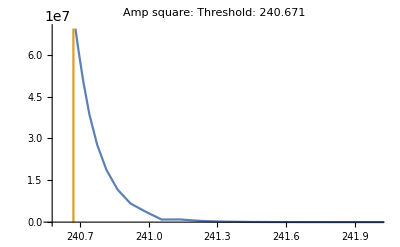

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Clear[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4,ΦB,ϕxB]
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
Mseq=Sequence[M1,M2,M3,M4];
```

Wavefunction build complete.

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x,y} = {0.999409304759193060376486206219937002970254980027675628662109375,0.0000129484} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26099×10^209 和 2.18188×10^209.

NIntegrate::ncvb: 在接近 {x,y} = {0.000590695,0.99998705161026963496755440557323124650679346814285963773727416992} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.25434×10^209-9.59962×10^195 ⅈ 和 2.17036×10^209.

2.66215×10^207+4.18059×10^191 ⅈ

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]+ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]+ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][M3,M4,M2,M1]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][M4,M3,M1,M2]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]+ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

9.45906×10^-11

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x,y} = {0.999409304759193060376486206219937002970254980027675628662109375,0.0000129484} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26099×10^209 和 2.18188×10^209.

NIntegrate::ncvb: 在接近 {x,y} = {0.000590695,0.99998705161026963496755440557323124650679346814285963773727416992} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.25434×10^209-9.59962×10^195 ⅈ 和 2.17036×10^209.

2.66215×10^207+4.18059×10^191 ⅈ

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x,y} = {0.999409304759193060376486206219937002970254980027675628662109375,0.0000129484} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26099×10^209 和 2.18188×10^209.

5.04402×10^209

```mathematica
Msumdat=Table[ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
Print["ω1=",ω1,"    ω2=",ω2];(*it's for debug purpose, you can comment this*){Sen,(Print@#;#)&@EXPR[ω1,ω2][M1,M2,M3,M4][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]],{ω1,0.4,ω1/.Last@FindMinimum[Sω1[ω1][Mseq],{ω1,0.99}],0.01}]
```

ω1=0.4    ω2=0.398562

0.0126772

ω1=0.41    ω2=0.408474

-0.0122517

ω1=0.42    ω2=0.418383

-0.0418249

ω1=0.43    ω2=0.428288

-0.0771114-1.42263×10^-23 ⅈ

ω1=0.44    ω2=0.438188

-0.119479-4.33705×10^-23 ⅈ

ω1=0.45    ω2=0.448084

-0.170692-3.45732×10^-23 ⅈ

ω1=0.46    ω2=0.457975

-0.233052-8.05812×10^-23 ⅈ

ω1=0.47    ω2=0.46786

-0.309586-5.03347×10^-22 ⅈ

ω1=0.48    ω2=0.477741

-0.404299-6.36674×10^-22 ⅈ

ω1=0.49    ω2=0.487616

-0.522461-5.33983×10^-22 ⅈ

ω1=0.5    ω2=0.497485

-0.670992-2.04943×10^-23 ⅈ

ω1=0.51    ω2=0.507348

-0.859035+4.32614×10^-22 ⅈ

ω1=0.52    ω2=0.517205

-1.09887+6.34422×10^-22 ⅈ

ω1=0.53    ω2=0.527054

-1.40727+3.43707×10^-21 ⅈ

ω1=0.54    ω2=0.536896

-1.80727+1.97904×10^-21 ⅈ

ω1=0.55    ω2=0.54673

-2.33083+1.2797×10^-22 ⅈ

ω1=0.56    ω2=0.556555

-3.02264+1.45164×10^-23 ⅈ

ω1=0.57    ω2=0.566372

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

-3.94587+4.92327×10^-22 ⅈ

ω1=0.58    ω2=0.576179

-5.19094+1.61906×10^-22 ⅈ

ω1=0.59    ω2=0.585975

-6.8889+4.94276×10^-23 ⅈ

ω1=0.6    ω2=0.595761

-9.23242+6.27469×10^-25 ⅈ

ω1=0.61    ω2=0.605535

-12.5089+2.21807×10^-25 ⅈ

ω1=0.62    ω2=0.615296

-17.1542+8.45662×10^-26 ⅈ

ω1=0.63    ω2=0.625043

-23.84

ω1=0.64    ω2=0.634775

-33.6207

ω1=0.65    ω2=0.644491

-48.1819

ω1=0.66    ω2=0.654189

-70.2694

ω1=0.67    ω2=0.663868

-104.442

ω1=0.68    ω2=0.673526

-158.404

ω1=0.69    ω2=0.683162

-245.404

ω1=0.7    ω2=0.692772

-388.558

ω1=0.71    ω2=0.702354

-628.699

ω1=0.72    ω2=0.711906

-1038.59

ω1=0.73    ω2=0.721423

-1748.49

ω1=0.74    ω2=0.730903

-2991.69

ω1=0.75    ω2=0.74034

-5183.99

ω1=0.76    ω2=0.749729

-9059.35

ω1=0.77    ω2=0.759065

-15893.8

ω1=0.78    ω2=0.768339

-27860.6

ω1=0.79    ω2=0.777544

-48565.3

ω1=0.8    ω2=0.786669

-83800.7

ω1=0.81    ω2=0.795701

-142523.

ω1=0.82    ω2=0.804625

-237967.

ω1=0.83    ω2=0.813423

-388664.

ω1=0.84    ω2=0.82207

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

-618938.

ω1=0.85    ω2=0.830539

-958244.

ω1=0.86    ω2=0.838789

-1.43858×10^6

ω1=0.87    ω2=0.846773

-2.0893×10^6

ω1=0.88    ω2=0.854424

-2.92916×10^6

ω1=0.89    ω2=0.861654

-3.95586×10^6

ω1=0.9    ω2=0.868338

-5.13466×10^6

ω1=0.91    ω2=0.874299

-6.38755×10^6

ω1=0.92    ω2=0.879272

-7.58394×10^6

ω1=0.93    ω2=0.882846

-8.53128×10^6

ω1=0.94    ω2=0.884345

-8.95918×10^6

{{266.58,0.0126772},{265.191,-0.0122517},{263.876,-0.0418249},{262.628,-0.0771114-1.42263×10^-23 ⅈ},{261.444,-0.119479-4.33705×10^-23 ⅈ},{260.32,-0.170692-3.45732×10^-23 ⅈ},{259.252,-0.233052-8.05812×10^-23 ⅈ},{258.238,-0.309586-5.03347×10^-22 ⅈ},{257.274,-0.404299-6.36674×10^-22 ⅈ},{256.357,-0.522461-5.33983×10^-22 ⅈ},{255.485,-0.670992-2.04943×10^-23 ⅈ},{254.656,-0.859035+4.32614×10^-22 ⅈ},{253.867,-1.09887+6.34422×10^-22 ⅈ},{253.116,-1.40727+3.43707×10^-21 ⅈ},{252.402,-1.80727+1.97904×10^-21 ⅈ},{251.722,-2.33083+1.2797×10^-22 ⅈ},{251.075,-3.02264+1.45164×10^-23 ⅈ},{250.459,-3.94587+4.92327×10^-22 ⅈ},{249.873,-5.19094+1.61906×10^-22 ⅈ},{249.316,-6.8889+4.94276×10^-23 ⅈ},{248.785,-9.23242+6.27469×10^-25 ⅈ},{248.281,-12.5089+2.21807×10^-25 ⅈ},{247.801,-17.1542+8.45662×10^-26 ⅈ},{247.345,-23.84},{246.911,-33.6207},{246.5,-48.1819},{246.108,-70.2694},{245.737,-104.442},{245.385,-158.404},{245.051,-245.404},{244.735,-388.558},{244.436,-628.699},{244.153,-1038.59},{243.885,-1748.49},{243.633,-2991.69},{243.395,-5183.99},{243.171,-9059.35},{242.96,-15893.8},{242.763,-27860.6},{242.578,-48565.3},{242.405,-83800.7},{242.243,-142523.},{242.094,-237967.},{241.955,-388664.},{241.826,-618938.},{241.709,-958244.},{241.601,-1.43858×10^6},{241.503,-2.0893×10^6},{241.416,-2.92916×10^6},{241.338,-3.95586×10^6},{241.27,-5.13466×10^6},{241.214,-6.38755×10^6},{241.169,-7.58394×10^6},{241.138,-8.53128×10^6},{241.125,-8.95918×10^6}}

```mathematica
Msumdat=Re@Msumdat;
```

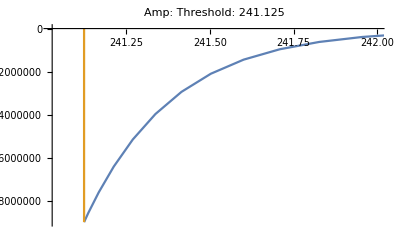

```mathematica
ListPlot[{Select[Re@Msumdat,#∈Reals&],{{M1+M2,0},{M1+M2,Last[Msumdat][[2]]}}},PlotRange->{{M1+M2-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[M1+M2]]
```

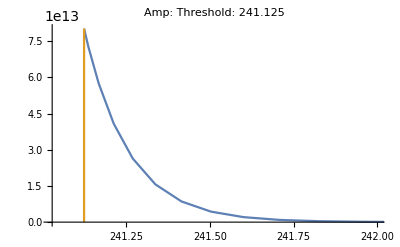

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat][[1]],(Transpose[Msumdat][[2]])^2},{{M1+M2,0},{M1+M2,(Last[Msumdat][[2]])^2}}},PlotRange->{{M1+M2-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[M1+M2]]
```

```mathematica
Table[Block[{ω2},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
Print["ω1=",ω1,"    ω2=",ω2];(*it's for debug purpose, you can comment this*){Sen,(Print@#;#)&@ℳone[ω1,ω2][M1,M2,M3,M4][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]],{ω1,0.4,ω1/.Last@FindMinimum[Sω1[ω1][Mseq],{ω1,0.99}],0.01}]
```

ω1=0.4    ω2=0.398562

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.0268661,0.000417732} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 5.4491419440909340382382425783772078458635348754810283664819156379×10^869-3.8400973775966317726789723988667816704560443632915069562703823584×10^856 ⅈ 和 1.0176379123125610661305274215012143162224981552578973087361864689×10^870.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

$Aborted

```mathematica
Block[{ω1=0.163,ω2},ω2=ω2p[ω1][Mseq]]
```

0.162794

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2p[ω1][Mseq];
EXPR[ω1,ω2][Mseq][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.0126772

```mathematica
Block[{ω1=0.4,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];
ℳone[ω1,ω2][Mseq][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.0268661,0.000417732} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 5.4491419440909340382382425783772078458635348754810283664819156379×10^869-3.8400973775966317726789723988667816704560443632915069562703823584×10^856 ⅈ 和 1.0176379123125610661305274215012143162224981552578973087361864689×10^870.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

$Aborted

```mathematica
Table[Block[{ω2},ω2=ω2p[ω1][M1,M2,M3,M4];
ℳone[ω1,ω2][Mseq][ϕ1,ϕ2,ϕ3,ϕ4]],{ω1,0.4,0.99,0.03}]
```

```mathematica
Block[{ω1=0.163,ω2},ℳone[ω1,ω2][M1,M2,M3,M4][ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2p[ω1][Mseq];ℳ1[Mseq][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

-1.17951×10^-7

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2p[ω1][Mseq];ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0

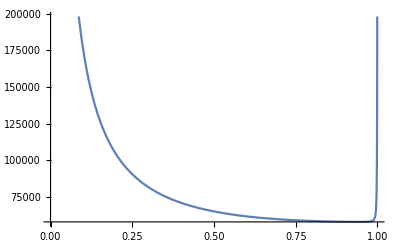

```mathematica
Plot[√(Sω1[ω1][Mseq]),{ω1,0,1}]
```

```mathematica
ω1/.Last@FindMinimum[Sω1[ω1][Mseq],{ω1,0.9}]
```

0.898903